```mathematica
FunctionExpand[-EulerGamma - 2*Log[2] - 2*Log[Gamma[3/4]/Gamma[1/4]]]
```

```mathematica
Limit[D[Gamma[u+1]PolyLog[u+1,E^(-Pi I/3)],u],u->0]
```

Limit[Gamma[1+u] PolyGamma[0,1+u] PolyLog[1+u,ⅇ^(-(ⅈ π)/3)]+Gamma[1+u] PolyLog^(1,0)[1+u,ⅇ^(-(ⅈ π)/3)],u→0]

```mathematica
-Pi Log[Gamma[1/4]^2/Pi/2/Sqrt[Pi]]/2//N
```

-0.260443

```mathematica
NIntegrate[Log@Log[1/x]/(1+x^2),{x,0,1}]
```

-0.260443

```mathematica
-Pi Log[Gamma[1/4]^2/Pi/2/Sqrt[Pi]]/2//FullSimplify
```

1/4 π Log[(4 π^3)/Gamma[1/4]^4]

```mathematica
FullSimplify[(StieltjesGamma[1,1/2+1/(4 p)]-StieltjesGamma[1,1/(4 p)])/(4 p)+((StieltjesGamma[0,1/2+1/(4 p)]-StieltjesGamma[0,1/(4 p)]) (Log[4 p]+EulerGamma))/(4 p)]
```

```mathematica
FullSimplify[-1/(4 p)((EulerGamma+Log[4 p]) (PolyGamma[0,1/4 (2+1/p)]-PolyGamma[0,1/(4 p)])-StieltjesGamma[1,1/4 (2+1/p)]+StieltjesGamma[1,1/(4 p)]),p>0]
```

-1/(4 p)((EulerGamma+Log[4 p]) (PolyGamma[0,1/4 (2+1/p)]-PolyGamma[0,1/(4 p)])-StieltjesGamma[1,1/4 (2+1/p)]+StieltjesGamma[1,1/(4 p)])

```mathematica
-k ((EulerGamma-Log[k]) (-PolyGamma[0,k]+PolyGamma[0,1/2+k])+StieltjesGamma[1,k]-StieltjesGamma[1,1/2+k])//FunctionExpand
```

```mathematica
k=3/2
NIntegrate[Log@Log[1/x]/(1+x^(1/(2k))),{x,0,1}]
-k ((-EulerGamma+Log[k]) PolyGamma[0,k]+(EulerGamma-Log[k]) PolyGamma[0,1/2+k]+StieltjesGamma[1,k]-StieltjesGamma[1,1/2+k])
Integrate[Log@Log[1/x]/(1+x^(1/(2k))),{x,0,1}]
{%,%%}//N
```

3/2

-0.257995

-3/2 ((1-EulerGamma) (EulerGamma-Log[3/2])+(-EulerGamma+Log[3/2]) PolyGamma[0,3/2]+StieltjesGamma[1,3/2]-StieltjesGamma[1,2])

3/2 (EulerGamma-Log[2]^2+Log[3] Log[4]-Log[6])

{-0.257995,-0.257995}

```mathematica
k=5/2
Integrate[Log@Log[1/x]/(1+x^(3)),{x,0,1}]
```

5/2

1/18 (-3 Log[2]^2+Log[3] Log[8]+√3 π (Log[128/27]+8 Log[π]-12 Log[Gamma[1/3]]))

```mathematica
NullSpace@{{2,0,1,-1,-3},{1,0,0,1,1},{-2,1,0,-2,0}}
```

{{-1,-2,5,0,1},{-1,0,3,1,0}}

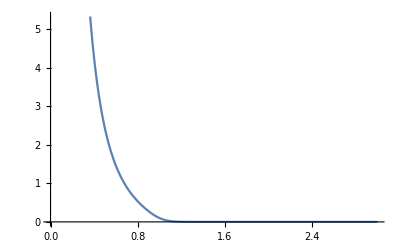

```mathematica
Plot[1/Total[x^Prime[Range@10]],{x,0,3}]
```

```mathematica
Sum[x^Prime[i],{i,1,Infinity}]
```

∑_(i=1)^∞ x^Prime[i]

```mathematica
扩域
```

```mathematica
NumberFieldIntegralBasis[2^(1/6)]
```

{1,AlgebraicNumber[Root[-2+#1^6&,2],{0,1,0,0,0,0}],AlgebraicNumber[Root[-2+#1^6&,2],{0,0,1,0,0,0}],AlgebraicNumber[Root[-2+#1^6&,2],{0,0,0,1,0,0}],AlgebraicNumber[Root[-2+#1^6&,2],{0,0,0,0,1,0}],AlgebraicNumber[Root[-2+#1^6&,2],{0,0,0,0,0,1}]}

```mathematica
elem=Alternatives@@Reverse@SortBy[StringLength]@Array[ElementData[#,"Symbol"]&,112];
chem=StringCases[#,e:elem~~n:DigitCharacter...:>{e,n}]/.""->"1"&;
group=List@@@Normal[GroupBy[#,First->Last,Total@ToExpression[#]&]]&
ChemicalSolver[input_List]:=Block[{all,elemts,null},all=group/@chem[ToString/@input];
elemts=Union[First@Transpose[Flatten[all,1]]];
null=NullSpace@Transpose[(elemts/.Rule@@@#&/@all)/._String->0];
Thread[input->Transpose@null]];
```

Apply[List,Normal[GroupBy[#1,First→Last,Total[ToExpression[#1]]&]],{1}]&

```mathematica
ChemicalSolver[{"KMnO4","H2SO4","H2O2","K2SO4","O2","H2O","MnSO4"}]
ChemicalSolver[{"KMnO4","H2SO4","K2SO4","O2","H2O","MnSO4"}]
ChemicalSolver[{"KMnO4","H2O2","K2SO4","O2","H2O","MnSO4"}]
ChemicalSolver[{"NaClO3","H2SO4","H2O2","ClO2","O2","H2O","Na2SO4"}]
ChemicalSolver[{"NaClO3","H2SO4","ClO2","O2","H2O","Na2SO4"}]
```

{KMnO4→{-2,0},H2SO4→{-3,0},H2O2→{3,-2},K2SO4→{1,0},O2→{1,1},H2O→{0,2},MnSO4→{2,0}}

{KMnO4→{-4},H2SO4→{-6},K2SO4→{2},O2→{5},H2O→{6},MnSO4→{4}}

{KMnO4→{0},H2O2→{-2},K2SO4→{0},O2→{1},H2O→{2},MnSO4→{0}}

{NaClO3→{-2,0},H2SO4→{-1,0},H2O2→{1,-2},ClO2→{2,0},O2→{0,1},H2O→{0,2},Na2SO4→{1,0}}

{NaClO3→{-4},H2SO4→{-2},ClO2→{4},O2→{1},H2O→{2},Na2SO4→{2}}

```mathematica
ChemicalSolver[{"CsB3H8","Cs2B9H9","Cs2B10H10","Cs2B12H12","CsBH4","H2"}]
```

{CsB3H8→{-2,-3,0},Cs2B9H9→{4,-14,2},Cs2B10H10→{-3,13,-3},Cs2B12H12→{0,0,1},CsBH4→{0,5,0},H2→{5,0,0}}

```mathematica
ChemicalSolver[{"P2I4","P4","H2O","PH4I","H3PO4"}]
ChemicalSolver[{"K2Cr2O7","H2SO4","Fe3O4","K2SO4","Cr2(S3O12)","H2O","Fe2(S3O12)"}]
ChemicalSolver[{"K4Fe(C6N6)","KMnO4","H2SO4","KHSO4","Fe2(S3O12)","MnSO4","HNO3","CO2","H2O"}]
```

{P2I4→{-10},P4→{-13},H2O→{-128},PH4I→{40},H3PO4→{32}}

{K2Cr2O7→{-1},H2SO4→{-31},Fe3O4→{-6},K2SO4→{1},Cr2(S3O12)→{1},H2O→{31},Fe2(S3O12)→{9}}

{K4Fe(C6N6)→{-10},KMnO4→{-122},H2SO4→{-299},KHSO4→{162},Fe2(S3O12)→{5},MnSO4→{122},HNO3→{60},CO2→{60},H2O→{188}}

```mathematica
ChemicalSolver[{"C","O2","CO","CO2"}]
```

{C→{-1,-2},O2→{-1,-1},CO→{0,2},CO2→{1,0}}

```mathematica
ChemicalSolver[{"ISb","IS","B"}]
ChemicalSolver[{"AbcD","Abc","D"}]
ChemicalSolver[{"(H10Cl10)","HCl"}]
```

{ISb→Transpose[{}],IS→Transpose[{}],B→Transpose[{}]}

{AbcD→Transpose[NullSpace[{}]],Abc→Transpose[NullSpace[{}]],D→Transpose[NullSpace[{}]]}

{(H10Cl10)→{-1},HCl→{10}}

```mathematica
$Line=0
```

0

a x+b y+c z

```mathematica
Inner
```

```mathematica
Inner[Times,{a,b,c},{x,y,z},List]
{a,b,c}*{x,y,z}
Inner[Times,{a,b,c},{x,y,z},Plus]
{a,b,c}.{x,y,z}
```

{a x,b y,c z}

{a x,b y,c z}

a x+b y+c z

a x+b y+c z

```mathematica
.
```

{a x,b y,c z}

```mathematica
$Line=0
```

0

```mathematica
Cross
```

```mathematica
Solve[E^x==a x,x]
```

{{x→-ProductLog[-1/a]}}

```mathematica
$Line=0
```

0

```mathematica
RSolve[{a[n+1]==(a[n]^3+a[n])/3,a[1]==1/2},a[n],n]
```

RSolve[{a[1+n]==1/3 (a[n]+a[n]^3),a[1]==1/2},a[n],n]

```mathematica
{Sin[t],Cos[t]}
```

{Sin[t],Cos[t]}

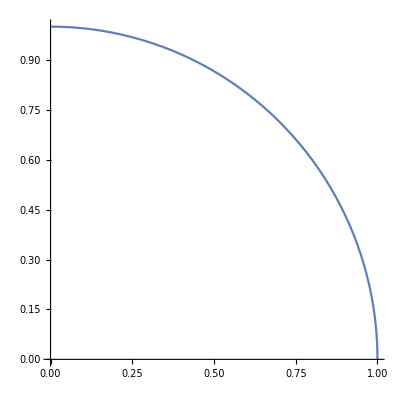

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,0,Pi/2}]
```

```mathematica
Triangle
```